## Problem statement

A TEC lumped parameter model is to be developed for a specific task: controlling the temperature of a jar of kefir, near room temperature. The works of Lineykin (2005, Analysis of thermoelectric coolers by a spice-compatible equivalent-circuit model) and Huang (2000, System dynamic model and temperature control of a thermoelectric cooler) informed this model, although it is distinct from them. In the end, five dependent sources were used. Note that Huang develops a transfer function model and ways to estimate parameters from TEC spec sheets and that Lineykin develops a lumped-parameter model. However, the following development is different in the following ways:
(1) it uses linear graph theory,
(2) it develops a (symbolic) nonlinear state model,
(3) it develops a (symbolic) linear state model,
(4) it gives the linearization symbolically such that any operating point can be used, and
(5) it does not assume qp1(t) = qp2(t), which I believe Lineykin does. It’s not a bad approximation, but it’s unnecessary.

-Graphics-

## State model

We will use the State package.

```mathematica
SetDirectory[NotebookDirectory[]];
<<State`
?stateEquations
?outEquations
?linearizeState
?linearizeOutput
```

stateEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the rhs of the state equations as a list.
N.b. can handle some nonlinear systems.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the output equations, use the function outEquations instead.
N.b. to linearize the returned state equations, use the function linearizeState.

outEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	outExps_List,   (* output expressions, e.g. vR2[t]+3*vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the rhs of the output equations as a list.
N.b. can handle some nonlinear systems.
N.b. can handle any expressions in outExps as long as they are expressed in terms of variables included in the
equations list. These are *not* limited to state variables! They can be primary or secondary and expressions thereof.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the state equations, use the function stateEquations instead.
N.b. to linearize the returned output equations, use the function linearizeOutput.

linearizeState[
	inVars_List, (* input variables *)
	inVarsOP_List, (* operating point for input variables *)
	stateVars_List, (* state variables *)
	stateVarsOP_List, (* operating point for state variables *)
	equations_List (* rhs of nonlinear (or linear) state equation *)
]
Returns an array containing the A and B matrices {A,B} of the input state equation
linearized about the input and state operating point.

linearizeOutput[
	inVars_List, (* input variables *)
	inVarsOP_List, (* operating point for input variables *)
	stateVars_List, (* state variables *)
	stateVarsOP_List, (* operating point for state variables *)
	equations_List (* rhs of nonlinear (or linear) output equation *)
]
Returns an array containing the C and D matrices {C,D} of the output equation
linearized about the input and state operating point.

```mathematica
inVars={
vs[t],
Ta[t]
};
stateVars={
vce[t],
Tc2[t],
Tc1[t],
Tcl[t]
};
outExp=stateVars~Join~{
v1[t],
qr1[t],
qp1[t],
qp2[t],
qj1[t],
qj2[t]
};
equations={
(* elemental *)
vce'[t] == 1/ce*ice[t],
Tc1'[t] == 1/c1*qc1[t],
Tc2'[t] == 1/c2*qc2[t],
Tcl'[t] == 1/cl*qcl[t],
vrs[t]==irs[t]*rs,
vrm[t]==irm[t]*rm,
Tr1[t]==qr1[t]*r1,
Tr2[t]==qr2[t]*r2,
Tr3[t]==qr3[t]*r3,
(* dependent sources *)
qj1[t]==vrm[t]*irm[t]/2,
qj2[t]==vrm[t]*irm[t]/2,
v1[t]==α*(Tc2[t]-Tc1[t]),
qp1[t]==α*irm[t]*Tc1[t],
qp2[t]==α*irm[t]*Tc2[t],
(* continuity *)
ice[t]==irs[t]-irm[t],
irm[t]==i1[t],
qc1[t]==qr1[t]-qr2[t]+qj2[t]-qp1[t],
qc2[t]==-qr1[t]-qr3[t]+qj2[t]+qp2[t],
qcl[t]==qr2[t],
(* compatibility *)
vrs[t]==vs[t]-vce[t],
vrm[t]==vce[t]-v1[t],
Tr1[t]==Tc2[t]-Tc1[t],
Tr2[t]==Tc1[t]-Tcl[t],
Tr3[t]==Tc2[t]-Ta[t]
};
ass={rs,r1,r2,r3,rm,cl,c1,c2,ce}//Thread[#>0]&;
n=Length[stateVars];
m=Length[outExp];
r=Length[inVars];
```

Find nonlinear state equation.

```mathematica
stateEqList=stateEquations[inVars,stateVars,equations]//Flatten;
stateEqList//Thread[D[stateVars,t]==#]&//TableForm
```

vce'[t]==-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)
Tc2'[t]==Ta[t]/(c2 r3)+Tc1[t]/(c2 r1)+(α^2 Tc1[t]^2)/(2 c2 rm)-((2 r1 rm+2 r3 rm) Tc2[t])/(2 c2 r1 r3 rm)-(α^2 Tc2[t]^2)/(2 c2 rm)+(α Tc1[t] vce[t])/(c2 rm)+vce[t]^2/(2 c2 rm)
Tc1'[t]==(-1/(c1 r1)-1/(c1 r2)) Tc1[t]-(α^2 Tc1[t]^2)/(2 c1 rm)+Tc2[t]/(c1 r1)+(α^2 Tc2[t]^2)/(2 c1 rm)+Tcl[t]/(c1 r2)-(α Tc2[t] vce[t])/(c1 rm)+vce[t]^2/(2 c1 rm)
Tcl'[t]==Tc1[t]/(cl r2)-Tcl[t]/(cl r2)

Linearize the state equation about operating point.

```mathematica
(* symbolic operating point for state variables (can be numeric) *)
x0=stateVars/.{x_[t]:>((ToString[x]<>"0")//ToExpression)} ;
(* symbolic operating point for input variables (can be numeric) *)
u0={vs0,Ta0}; 
dx=stateVars/.{x_[t]:>(("d"<>ToString[x[t]])//ToExpression)};
du=inVars/.{x_[t]:>(("d"<>ToString[x[t]])//ToExpression)};
ab=linearizeState[inVars,u0,stateVars,x0,stateEqList];
a=ab[[1]];b=ab[[2]];
a//MatrixForm//Print["A = ",#]&
b//MatrixForm//Print["B = ",#]&
D[dx,t]//MatrixForm//#==A.MatrixForm[dx]+B.MatrixForm[du]&
```

A = (-(rm+rs)/(ce rm rs) | α/(ce rm) | -α/(ce rm) | 0
vce0/(c2 rm)+(Tc10 α)/(c2 rm) | -(2 r1 rm+2 r3 rm)/(2 c2 r1 r3 rm)-(Tc20 α^2)/(c2 rm) | 1/(c2 r1)+(vce0 α)/(c2 rm)+(Tc10 α^2)/(c2 rm) | 0
vce0/(c1 rm)-(Tc20 α)/(c1 rm) | 1/(c1 r1)-(vce0 α)/(c1 rm)+(Tc20 α^2)/(c1 rm) | -1/(c1 r1)-1/(c1 r2)-(Tc10 α^2)/(c1 rm) | 1/(c1 r2)
0 | 0 | 1/(cl r2) | -1/(cl r2))

B = (1/(ce rs) | 0
0 | 1/(c2 r3)
0 | 0
0 | 0)

(dvce'[t]
dTc2'[t]
dTc1'[t]
dTcl'[t])==A.(dvce[t]
dTc2[t]
dTc1[t]
dTcl[t])+B.(dvs[t]
dTa[t])

Find the output equation.

```mathematica
outEqList = outEquations[inVars,stateVars,outExp,equations];
Map[ToString,outExp]//Thread[#==outEqList]&//TableForm
```

vce[t]==vce[t]
Tc2[t]==Tc2[t]
Tc1[t]==Tc1[t]
Tcl[t]==Tcl[t]
v1[t]==-α Tc1[t]+α Tc2[t]
qr1[t]==-Tc1[t]/r1+Tc2[t]/r1
qp1[t]==(α^2 Tc1[t]^2)/rm-(α^2 Tc1[t] Tc2[t])/rm+(α Tc1[t] vce[t])/rm
qp2[t]==(α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(α Tc2[t] vce[t])/rm
qj1[t]==(α^2 Tc1[t]^2)/(2 rm)-(α^2 Tc1[t] Tc2[t])/rm+(α^2 Tc2[t]^2)/(2 rm)+((α Tc1[t])/rm-(α Tc2[t])/rm) vce[t]+vce[t]^2/(2 rm)
qj2[t]==(α^2 Tc1[t]^2)/(2 rm)-(α^2 Tc1[t] Tc2[t])/rm+(α^2 Tc2[t]^2)/(2 rm)+((α Tc1[t])/rm-(α Tc2[t])/rm) vce[t]+vce[t]^2/(2 rm)

Linearize output equation about operating point.

```mathematica
cd=linearizeOutput[inVars,u0,stateVars,x0,outEqList];
c=cd[[1]];d=cd[[2]];
c//MatrixForm//Print["C = ",#]&
d//MatrixForm//Print["D = ",#]&
outExp//MatrixForm//#==C.MatrixForm[dx]+D.MatrixForm[du]&
```

C = (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | α | -α | 0
0 | 1/r1 | -1/r1 | 0
(Tc10 α)/rm | -(Tc10 α^2)/rm | (vce0 α)/rm+(2 Tc10 α^2)/rm-(Tc20 α^2)/rm | 0
(Tc20 α)/rm | (vce0 α)/rm+(Tc10 α^2)/rm-(2 Tc20 α^2)/rm | (Tc20 α^2)/rm | 0
vce0/rm+(Tc10 α)/rm-(Tc20 α)/rm | -(vce0 α)/rm-(Tc10 α^2)/rm+(Tc20 α^2)/rm | (vce0 α)/rm+(Tc10 α^2)/rm-(Tc20 α^2)/rm | 0
vce0/rm+(Tc10 α)/rm-(Tc20 α)/rm | -(vce0 α)/rm-(Tc10 α^2)/rm+(Tc20 α^2)/rm | (vce0 α)/rm+(Tc10 α^2)/rm-(Tc20 α^2)/rm | 0)

D = (0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

(vce[t]
Tc2[t]
Tc1[t]
Tcl[t]
v1[t]
qr1[t]
qp1[t]
qp2[t]
qj1[t]
qj2[t])==C.(dvce[t]
dTc2[t]
dTc1[t]
dTcl[t])+D.(dvs[t]
dTa[t])

Form nonlinear and linear state models for MMA.

```mathematica
nsys=NonlinearStateSpaceModel[{stateEqList,outEqList},stateVars,inVars]
sys=StateSpaceModel[{a.dx+b.du,c.dx+d.du},dx,du]
tf=TransferFunctionModel[sys,s]
```

-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)Ta[t]/(c2 r3)+Tc1[t]/(c2 r1)+(α^2 Tc1[t]^2)/(2 c2 rm)-((2 r1 rm+2 r3 rm) Tc2[t])/(2 c2 r1 r3 rm)-(α^2 Tc2[t]^2)/(2 c2 rm)+(α Tc1[t] vce[t])/(c2 rm)+vce[t]^2/(2 c2 rm)(-1/(c1 r1)-1/(c1 r2)) Tc1[t]-(α^2 Tc1[t]^2)/(2 c1 rm)+Tc2[t]/(c1 r1)+(α^2 Tc2[t]^2)/(2 c1 rm)+Tcl[t]/(c1 r2)-(α Tc2[t] vce[t])/(c1 rm)+vce[t]^2/(2 c1 rm)Tc1[t]/(cl r2)-Tcl[t]/(cl r2)vce[t]Tc2[t]Tc1[t]Tcl[t]-α Tc1[t]+α Tc2[t]-Tc1[t]/r1+Tc2[t]/r1(α^2 Tc1[t]^2)/rm-(α^2 Tc1[t] Tc2[t])/rm+(α Tc1[t] vce[t])/rm(α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(α Tc2[t] vce[t])/rm(α^2 Tc1[t]^2)/(2 rm)-(α^2 Tc1[t] Tc2[t])/rm+(α^2 Tc2[t]^2)/(2 rm)+((α Tc1[t])/rm-(α Tc2[t])/rm) vce[t]+vce[t]^2/(2 rm)(α^2 Tc1[t]^2)/(2 rm)-(α^2 Tc1[t] Tc2[t])/rm+(α^2 Tc2[t]^2)/(2 rm)+((α Tc1[t])/rm-(α Tc2[t])/rm) vce[t]+vce[t]^2/(2 rm)vce[t]Tc2[t]Tc1[t]Tcl[t] 421010NoneNoneFalseFalseFalse{vs[t],Ta[t]}Automatic

-(rm+rs)/(ce rm rs)α/(ce rm)-α/(ce rm)01/(ce rs)0vce0/(c2 rm)+(Tc10 α)/(c2 rm)-(2 r1 rm+2 r3 rm)/(2 c2 r1 r3 rm)-(Tc20 α^2)/(c2 rm)1/(c2 r1)+(vce0 α)/(c2 rm)+(Tc10 α^2)/(c2 rm)001/(c2 r3)vce0/(c1 rm)-(Tc20 α)/(c1 rm)1/(c1 r1)-(vce0 α)/(c1 rm)+(Tc20 α^2)/(c1 rm)-1/(c1 r1)-1/(c1 r2)-(Tc10 α^2)/(c1 rm)1/(c1 r2)00001/(cl r2)-1/(cl r2)001000000100000010000001000α-α00001/r1-1/r1000(Tc10 α)/rm-(Tc10 α^2)/rm(vce0 α)/rm+(2 Tc10 α^2)/rm-(Tc20 α^2)/rm000(Tc20 α)/rm(vce0 α)/rm+(Tc10 α^2)/rm-(2 Tc20 α^2)/rm(Tc20 α^2)/rm000vce0/rm+(Tc10 α)/rm-(Tc20 α)/rm-(vce0 α)/rm-(Tc10 α^2)/rm+(Tc20 α^2)/rm(vce0 α)/rm+(Tc10 α^2)/rm-(Tc20 α^2)/rm000vce0/rm+(Tc10 α)/rm-(Tc20 α)/rm-(vce0 α)/rm-(Tc10 α^2)/rm+(Tc20 α^2)/rm(vce0 α)/rm+(Tc10 α^2)/rm-(Tc20 α^2)/rm000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic21041FalseFalseFalseAutomaticNone,{{dvce[t],0},{dTc2[t],0},{dTc1[t],0},{dTcl[t],0}},{{dvs[t],0},{dTa[t],0}}

(rm (rm^2+r1 rm Tc10 α^2+r1 r3 vce0^2 α^2+r1 r3 Tc10 vce0 α^3-r1 r3 Tc20 vce0 α^3+c1 r1 rm^2 s+cl r1 rm^2 s+cl r2 rm^2 s+c1 r3 rm^2 s+c2 r3 rm^2 s+cl r3 rm^2 s+cl r1 r2 rm Tc10 α^2 s+c2 r1 r3 rm Tc10 α^2 s+c1 r1 r3 rm Tc20 α^2 s+cl r1 r3 rm Tc20 α^2 s+cl r1 r2 r3 vce0^2 α^2 s+cl r1 r2 r3 Tc10 vce0 α^3 s-cl r1 r2 r3 Tc20 vce0 α^3 s+c1 cl r1 r2 rm^2 s^2+c1 c2 r1 r3 rm^2 s^2+c2 cl r1 r3 rm^2 s^2+c1 cl r2 r3 rm^2 s^2+c2 cl r2 r3 rm^2 s^2+c2 cl r1 r2 r3 rm Tc10 α^2 s^2+c1 cl r1 r2 r3 rm Tc20 α^2 s^2+c1 c2 cl r1 r2 r3 rm^2 s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm rs (vce0 α^2+Tc10 α^3-Tc20 α^3+c1 rm α s+cl rm α s+cl r2 vce0 α^2 s+cl r2 Tc10 α^3 s-cl r2 Tc20 α^3 s+c1 cl r2 rm α s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r3 rm (2 rm vce0+rm Tc10 α-rm Tc20 α+r1 vce0^2 α+2 r1 Tc10 vce0 α^2-r1 Tc20 vce0 α^2+r1 Tc10^2 α^3-r1 Tc10 Tc20 α^3+c1 r1 rm vce0 s+cl r1 rm vce0 s+2 cl r2 rm vce0 s+c1 r1 rm Tc10 α s+cl r1 rm Tc10 α s+cl r2 rm Tc10 α s-cl r2 rm Tc20 α s+cl r1 r2 vce0^2 α s+2 cl r1 r2 Tc10 vce0 α^2 s-cl r1 r2 Tc20 vce0 α^2 s+cl r1 r2 Tc10^2 α^3 s-cl r1 r2 Tc10 Tc20 α^3 s+c1 cl r1 r2 rm vce0 s^2+c1 cl r1 r2 rm Tc10 α s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (rm^2+rm rs+r1 rs vce0 α+r1 rm Tc10 α^2+r1 rs Tc10 α^2-r1 rs Tc20 α^2+c1 r1 rm^2 s+cl r1 rm^2 s+cl r2 rm^2 s+c1 r1 rm rs s+cl r1 rm rs s+cl r2 rm rs s+ce rm^2 rs s+cl r1 r2 rs vce0 α s+cl r1 r2 rm Tc10 α^2 s+cl r1 r2 rs Tc10 α^2 s+ce r1 rm rs Tc10 α^2 s-cl r1 r2 rs Tc20 α^2 s+c1 cl r1 r2 rm^2 s^2+c1 cl r1 r2 rm rs s^2+c1 ce r1 rm^2 rs s^2+ce cl r1 rm^2 rs s^2+ce cl r2 rm^2 rs s^2+ce cl r1 r2 rm rs Tc10 α^2 s^2+c1 ce cl r1 r2 rm^2 rs s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (-r1 rm vce0-2 r3 rm vce0-r3 rm Tc10 α+r1 rm Tc20 α+r3 rm Tc20 α+r1 r3 vce0^2 α+r1 r3 Tc10 vce0 α^2-2 r1 r3 Tc20 vce0 α^2-r1 r3 Tc10 Tc20 α^3+r1 r3 Tc20^2 α^3-cl r1 r2 rm vce0 s-c2 r1 r3 rm vce0 s-2 cl r2 r3 rm vce0 s-cl r2 r3 rm Tc10 α s+cl r1 r2 rm Tc20 α s+c2 r1 r3 rm Tc20 α s+cl r2 r3 rm Tc20 α s+cl r1 r2 r3 vce0^2 α s+cl r1 r2 r3 Tc10 vce0 α^2 s-2 cl r1 r2 r3 Tc20 vce0 α^2 s-cl r1 r2 r3 Tc10 Tc20 α^3 s+cl r1 r2 r3 Tc20^2 α^3 s-c2 cl r1 r2 r3 rm vce0 s^2+c2 cl r1 r2 r3 rm Tc20 α s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 (rm+rs-r1 vce0 α+r1 Tc20 α^2+cl r2 rm s+cl r2 rs s+ce rm rs s-cl r1 r2 vce0 α s-ce r1 rs vce0 α s+cl r1 r2 Tc20 α^2 s+ce r1 rs Tc20 α^2 s+ce cl r2 rm rs s^2-ce cl r1 r2 rs vce0 α s^2+ce cl r1 r2 rs Tc20 α^2 s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (-r1 rm vce0-2 r3 rm vce0-r3 rm Tc10 α+r1 rm Tc20 α+r3 rm Tc20 α+r1 r3 vce0^2 α+r1 r3 Tc10 vce0 α^2-2 r1 r3 Tc20 vce0 α^2-r1 r3 Tc10 Tc20 α^3+r1 r3 Tc20^2 α^3-c2 r1 r3 rm vce0 s+c2 r1 r3 rm Tc20 α s))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 (rm+rs-r1 vce0 α+r1 Tc20 α^2+ce rm rs s-ce r1 rs vce0 α s+ce r1 rs Tc20 α^2 s))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm (-rm vce0 α+rm Tc20 α^2+2 r3 vce0^2 α^2+3 r3 Tc10 vce0 α^3-3 r3 Tc20 vce0 α^3+r3 Tc10^2 α^4-2 r3 Tc10 Tc20 α^4+r3 Tc20^2 α^4-cl r2 rm vce0 α s+c1 r3 rm vce0 α s-c2 r3 rm vce0 α s+cl r3 rm vce0 α s+c1 r3 rm Tc10 α^2 s+cl r3 rm Tc10 α^2 s+cl r2 rm Tc20 α^2 s+c2 r3 rm Tc20 α^2 s+2 cl r2 r3 vce0^2 α^2 s+3 cl r2 r3 Tc10 vce0 α^3 s-3 cl r2 r3 Tc20 vce0 α^3 s+cl r2 r3 Tc10^2 α^4 s-2 cl r2 r3 Tc10 Tc20 α^4 s+cl r2 r3 Tc20^2 α^4 s+c1 cl r2 r3 rm vce0 α s^2-c2 cl r2 r3 rm vce0 α s^2+c1 cl r2 r3 rm Tc10 α^2 s^2+c2 cl r2 r3 rm Tc20 α^2 s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm (rm vce0 α^2+rs vce0 α^2+rm Tc10 α^3+rs Tc10 α^3-rm Tc20 α^3-rs Tc20 α^3+c1 rm^2 α s+cl rm^2 α s+c1 rm rs α s+cl rm rs α s+cl r2 rm vce0 α^2 s+cl r2 rs vce0 α^2 s+ce rm rs vce0 α^2 s+cl r2 rm Tc10 α^3 s+cl r2 rs Tc10 α^3 s+ce rm rs Tc10 α^3 s-cl r2 rm Tc20 α^3 s-cl r2 rs Tc20 α^3 s-ce rm rs Tc20 α^3 s+c1 cl r2 rm^2 α s^2+c1 cl r2 rm rs α s^2+c1 ce rm^2 rs α s^2+ce cl rm^2 rs α s^2+ce cl r2 rm rs vce0 α^2 s^2+ce cl r2 rm rs Tc10 α^3 s^2-ce cl r2 rm rs Tc20 α^3 s^2+c1 ce cl r2 rm^2 rs α s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (-rm vce0+rm Tc20 α+2 r3 vce0^2 α+3 r3 Tc10 vce0 α^2-3 r3 Tc20 vce0 α^2+r3 Tc10^2 α^3-2 r3 Tc10 Tc20 α^3+r3 Tc20^2 α^3-cl r2 rm vce0 s+c1 r3 rm vce0 s-c2 r3 rm vce0 s+cl r3 rm vce0 s+c1 r3 rm Tc10 α s+cl r3 rm Tc10 α s+cl r2 rm Tc20 α s+c2 r3 rm Tc20 α s+2 cl r2 r3 vce0^2 α s+3 cl r2 r3 Tc10 vce0 α^2 s-3 cl r2 r3 Tc20 vce0 α^2 s+cl r2 r3 Tc10^2 α^3 s-2 cl r2 r3 Tc10 Tc20 α^3 s+cl r2 r3 Tc20^2 α^3 s+c1 cl r2 r3 rm vce0 s^2-c2 cl r2 r3 rm vce0 s^2+c1 cl r2 r3 rm Tc10 α s^2+c2 cl r2 r3 rm Tc20 α s^2))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (rm vce0 α+rs vce0 α+rm Tc10 α^2+rs Tc10 α^2-rm Tc20 α^2-rs Tc20 α^2+c1 rm^2 s+cl rm^2 s+c1 rm rs s+cl rm rs s+cl r2 rm vce0 α s+cl r2 rs vce0 α s+ce rm rs vce0 α s+cl r2 rm Tc10 α^2 s+cl r2 rs Tc10 α^2 s+ce rm rs Tc10 α^2 s-cl r2 rm Tc20 α^2 s-cl r2 rs Tc20 α^2 s-ce rm rs Tc20 α^2 s+c1 cl r2 rm^2 s^2+c1 cl r2 rm rs s^2+c1 ce rm^2 rs s^2+ce cl rm^2 rs s^2+ce cl r2 rm rs vce0 α s^2+ce cl r2 rm rs Tc10 α^2 s^2-ce cl r2 rm rs Tc20 α^2 s^2+c1 ce cl r2 rm^2 rs s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 Tc10 α+r1 rm vce0^2 α+2 r3 rm vce0^2 α+2 r1 rm Tc10 vce0 α^2+3 r3 rm Tc10 vce0 α^2-2 r1 rm Tc20 vce0 α^2-3 r3 rm Tc20 vce0 α^2-r1 r3 vce0^3 α^2+r1 rm Tc10^2 α^3+r3 rm Tc10^2 α^3-2 r1 rm Tc10 Tc20 α^3-2 r3 rm Tc10 Tc20 α^3+r1 rm Tc20^2 α^3+r3 rm Tc20^2 α^3-3 r1 r3 Tc10 vce0^2 α^3+3 r1 r3 Tc20 vce0^2 α^3-3 r1 r3 Tc10^2 vce0 α^4+6 r1 r3 Tc10 Tc20 vce0 α^4-3 r1 r3 Tc20^2 vce0 α^4-r1 r3 Tc10^3 α^5+3 r1 r3 Tc10^2 Tc20 α^5-3 r1 r3 Tc10 Tc20^2 α^5+r1 r3 Tc20^3 α^5+c1 r1 rm^2 Tc10 α s+cl r1 rm^2 Tc10 α s+cl r2 rm^2 Tc10 α s+c1 r3 rm^2 Tc10 α s+c2 r3 rm^2 Tc10 α s+cl r3 rm^2 Tc10 α s+cl r1 r2 rm vce0^2 α s+c2 r1 r3 rm vce0^2 α s+2 cl r2 r3 rm vce0^2 α s+2 cl r1 r2 rm Tc10 vce0 α^2 s-c1 r1 r3 rm Tc10 vce0 α^2 s+2 c2 r1 r3 rm Tc10 vce0 α^2 s-cl r1 r3 rm Tc10 vce0 α^2 s+3 cl r2 r3 rm Tc10 vce0 α^2 s-2 cl r1 r2 rm Tc20 vce0 α^2 s-2 c2 r1 r3 rm Tc20 vce0 α^2 s-3 cl r2 r3 rm Tc20 vce0 α^2 s-cl r1 r2 r3 vce0^3 α^2 s+cl r1 r2 rm Tc10^2 α^3 s-c1 r1 r3 rm Tc10^2 α^3 s+c2 r1 r3 rm Tc10^2 α^3 s-cl r1 r3 rm Tc10^2 α^3 s+cl r2 r3 rm Tc10^2 α^3 s-2 cl r1 r2 rm Tc10 Tc20 α^3 s+c1 r1 r3 rm Tc10 Tc20 α^3 s-2 c2 r1 r3 rm Tc10 Tc20 α^3 s+cl r1 r3 rm Tc10 Tc20 α^3 s-2 cl r2 r3 rm Tc10 Tc20 α^3 s+cl r1 r2 rm Tc20^2 α^3 s+c2 r1 r3 rm Tc20^2 α^3 s+cl r2 r3 rm Tc20^2 α^3 s-3 cl r1 r2 r3 Tc10 vce0^2 α^3 s+3 cl r1 r2 r3 Tc20 vce0^2 α^3 s-3 cl r1 r2 r3 Tc10^2 vce0 α^4 s+6 cl r1 r2 r3 Tc10 Tc20 vce0 α^4 s-3 cl r1 r2 r3 Tc20^2 vce0 α^4 s-cl r1 r2 r3 Tc10^3 α^5 s+3 cl r1 r2 r3 Tc10^2 Tc20 α^5 s-3 cl r1 r2 r3 Tc10 Tc20^2 α^5 s+cl r1 r2 r3 Tc20^3 α^5 s+c1 cl r1 r2 rm^2 Tc10 α s^2+c1 c2 r1 r3 rm^2 Tc10 α s^2+c2 cl r1 r3 rm^2 Tc10 α s^2+c1 cl r2 r3 rm^2 Tc10 α s^2+c2 cl r2 r3 rm^2 Tc10 α s^2+c2 cl r1 r2 r3 rm vce0^2 α s^2-c1 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2+2 c2 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2-2 c2 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2-c1 cl r1 r2 r3 rm Tc10^2 α^3 s^2+c2 cl r1 r2 r3 rm Tc10^2 α^3 s^2+c1 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2-2 c2 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2+c2 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c1 c2 cl r1 r2 r3 rm^2 Tc10 α s^3)/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (-rm vce0 α-rs vce0 α-rm Tc10 α^2-rs Tc10 α^2+rm Tc20 α^2+rs Tc20 α^2+r1 vce0^2 α^2+2 r1 Tc10 vce0 α^3-2 r1 Tc20 vce0 α^3+r1 Tc10^2 α^4-2 r1 Tc10 Tc20 α^4+r1 Tc20^2 α^4-cl r2 rm vce0 α s-cl r2 rs vce0 α s-ce rm rs vce0 α s+c1 r1 rm Tc10 α^2 s+cl r1 rm Tc10 α^2 s-cl r2 rm Tc10 α^2 s-cl r2 rs Tc10 α^2 s-ce rm rs Tc10 α^2 s+cl r2 rm Tc20 α^2 s+cl r2 rs Tc20 α^2 s+ce rm rs Tc20 α^2 s+cl r1 r2 vce0^2 α^2 s+ce r1 rs vce0^2 α^2 s+2 cl r1 r2 Tc10 vce0 α^3 s+2 ce r1 rs Tc10 vce0 α^3 s-2 cl r1 r2 Tc20 vce0 α^3 s-2 ce r1 rs Tc20 vce0 α^3 s+cl r1 r2 Tc10^2 α^4 s+ce r1 rs Tc10^2 α^4 s-2 cl r1 r2 Tc10 Tc20 α^4 s-2 ce r1 rs Tc10 Tc20 α^4 s+cl r1 r2 Tc20^2 α^4 s+ce r1 rs Tc20^2 α^4 s-ce cl r2 rm rs vce0 α s^2+c1 cl r1 r2 rm Tc10 α^2 s^2+c1 ce r1 rm rs Tc10 α^2 s^2+ce cl r1 rm rs Tc10 α^2 s^2-ce cl r2 rm rs Tc10 α^2 s^2+ce cl r2 rm rs Tc20 α^2 s^2+ce cl r1 r2 rs vce0^2 α^2 s^2+2 ce cl r1 r2 rs Tc10 vce0 α^3 s^2-2 ce cl r1 r2 rs Tc20 vce0 α^3 s^2+ce cl r1 r2 rs Tc10^2 α^4 s^2-2 ce cl r1 r2 rs Tc10 Tc20 α^4 s^2+ce cl r1 r2 rs Tc20^2 α^4 s^2+c1 ce cl r1 r2 rm rs Tc10 α^2 s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 Tc20 α+2 r3 rm vce0^2 α+3 r3 rm Tc10 vce0 α^2+r1 rm Tc20 vce0 α^2-3 r3 rm Tc20 vce0 α^2+r1 r3 vce0^3 α^2+r3 rm Tc10^2 α^3+r1 rm Tc10 Tc20 α^3-2 r3 rm Tc10 Tc20 α^3-r1 rm Tc20^2 α^3+r3 rm Tc20^2 α^3+3 r1 r3 Tc10 vce0^2 α^3-3 r1 r3 Tc20 vce0^2 α^3+3 r1 r3 Tc10^2 vce0 α^4-6 r1 r3 Tc10 Tc20 vce0 α^4+3 r1 r3 Tc20^2 vce0 α^4+r1 r3 Tc10^3 α^5-3 r1 r3 Tc10^2 Tc20 α^5+3 r1 r3 Tc10 Tc20^2 α^5-r1 r3 Tc20^3 α^5+c1 r1 rm^2 Tc20 α s+cl r1 rm^2 Tc20 α s+cl r2 rm^2 Tc20 α s+c1 r3 rm^2 Tc20 α s+c2 r3 rm^2 Tc20 α s+cl r3 rm^2 Tc20 α s+c1 r1 r3 rm vce0^2 α s+cl r1 r3 rm vce0^2 α s+2 cl r2 r3 rm vce0^2 α s+2 c1 r1 r3 rm Tc10 vce0 α^2 s+2 cl r1 r3 rm Tc10 vce0 α^2 s+3 cl r2 r3 rm Tc10 vce0 α^2 s+cl r1 r2 rm Tc20 vce0 α^2 s-2 c1 r1 r3 rm Tc20 vce0 α^2 s+c2 r1 r3 rm Tc20 vce0 α^2 s-2 cl r1 r3 rm Tc20 vce0 α^2 s-3 cl r2 r3 rm Tc20 vce0 α^2 s+cl r1 r2 r3 vce0^3 α^2 s+c1 r1 r3 rm Tc10^2 α^3 s+cl r1 r3 rm Tc10^2 α^3 s+cl r2 r3 rm Tc10^2 α^3 s+cl r1 r2 rm Tc10 Tc20 α^3 s-2 c1 r1 r3 rm Tc10 Tc20 α^3 s+c2 r1 r3 rm Tc10 Tc20 α^3 s-2 cl r1 r3 rm Tc10 Tc20 α^3 s-2 cl r2 r3 rm Tc10 Tc20 α^3 s-cl r1 r2 rm Tc20^2 α^3 s+c1 r1 r3 rm Tc20^2 α^3 s-c2 r1 r3 rm Tc20^2 α^3 s+cl r1 r3 rm Tc20^2 α^3 s+cl r2 r3 rm Tc20^2 α^3 s+3 cl r1 r2 r3 Tc10 vce0^2 α^3 s-3 cl r1 r2 r3 Tc20 vce0^2 α^3 s+3 cl r1 r2 r3 Tc10^2 vce0 α^4 s-6 cl r1 r2 r3 Tc10 Tc20 vce0 α^4 s+3 cl r1 r2 r3 Tc20^2 vce0 α^4 s+cl r1 r2 r3 Tc10^3 α^5 s-3 cl r1 r2 r3 Tc10^2 Tc20 α^5 s+3 cl r1 r2 r3 Tc10 Tc20^2 α^5 s-cl r1 r2 r3 Tc20^3 α^5 s+c1 cl r1 r2 rm^2 Tc20 α s^2+c1 c2 r1 r3 rm^2 Tc20 α s^2+c2 cl r1 r3 rm^2 Tc20 α s^2+c1 cl r2 r3 rm^2 Tc20 α s^2+c2 cl r2 r3 rm^2 Tc20 α s^2+c1 cl r1 r2 r3 rm vce0^2 α s^2+2 c1 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2-2 c1 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2+c2 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2+c1 cl r1 r2 r3 rm Tc10^2 α^3 s^2-2 c1 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2+c2 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2+c1 cl r1 r2 r3 rm Tc20^2 α^3 s^2-c2 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c1 c2 cl r1 r2 r3 rm^2 Tc20 α s^3)/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 vce0 α+rm rs vce0 α+rm^2 Tc10 α^2+rm rs Tc10 α^2-rm^2 Tc20 α^2-rm rs Tc20 α^2+r1 rs vce0^2 α^2+r1 rm Tc10 vce0 α^3+2 r1 rs Tc10 vce0 α^3-r1 rm Tc20 vce0 α^3-2 r1 rs Tc20 vce0 α^3+r1 rm Tc10^2 α^4+r1 rs Tc10^2 α^4-2 r1 rm Tc10 Tc20 α^4-2 r1 rs Tc10 Tc20 α^4+r1 rm Tc20^2 α^4+r1 rs Tc20^2 α^4+c1 r1 rm^2 vce0 α s+cl r1 rm^2 vce0 α s+cl r2 rm^2 vce0 α s+c1 r1 rm rs vce0 α s+cl r1 rm rs vce0 α s+cl r2 rm rs vce0 α s+ce rm^2 rs vce0 α s+c1 r1 rm^2 Tc10 α^2 s+cl r1 rm^2 Tc10 α^2 s+cl r2 rm^2 Tc10 α^2 s+c1 r1 rm rs Tc10 α^2 s+cl r1 rm rs Tc10 α^2 s+cl r2 rm rs Tc10 α^2 s+ce rm^2 rs Tc10 α^2 s-2 c1 r1 rm^2 Tc20 α^2 s-2 cl r1 rm^2 Tc20 α^2 s-cl r2 rm^2 Tc20 α^2 s-c1 r1 rm rs Tc20 α^2 s-cl r1 rm rs Tc20 α^2 s-cl r2 rm rs Tc20 α^2 s-ce rm^2 rs Tc20 α^2 s+cl r1 r2 rs vce0^2 α^2 s+cl r1 r2 rm Tc10 vce0 α^3 s+2 cl r1 r2 rs Tc10 vce0 α^3 s+ce r1 rm rs Tc10 vce0 α^3 s-cl r1 r2 rm Tc20 vce0 α^3 s-2 cl r1 r2 rs Tc20 vce0 α^3 s-ce r1 rm rs Tc20 vce0 α^3 s+cl r1 r2 rm Tc10^2 α^4 s+cl r1 r2 rs Tc10^2 α^4 s+ce r1 rm rs Tc10^2 α^4 s-2 cl r1 r2 rm Tc10 Tc20 α^4 s-2 cl r1 r2 rs Tc10 Tc20 α^4 s-2 ce r1 rm rs Tc10 Tc20 α^4 s+cl r1 r2 rm Tc20^2 α^4 s+cl r1 r2 rs Tc20^2 α^4 s+ce r1 rm rs Tc20^2 α^4 s+c1 cl r1 r2 rm^2 vce0 α s^2+c1 cl r1 r2 rm rs vce0 α s^2+c1 ce r1 rm^2 rs vce0 α s^2+ce cl r1 rm^2 rs vce0 α s^2+ce cl r2 rm^2 rs vce0 α s^2+c1 cl r1 r2 rm^2 Tc10 α^2 s^2+c1 cl r1 r2 rm rs Tc10 α^2 s^2+c1 ce r1 rm^2 rs Tc10 α^2 s^2+ce cl r1 rm^2 rs Tc10 α^2 s^2+ce cl r2 rm^2 rs Tc10 α^2 s^2-2 c1 cl r1 r2 rm^2 Tc20 α^2 s^2-c1 cl r1 r2 rm rs Tc20 α^2 s^2-2 c1 ce r1 rm^2 rs Tc20 α^2 s^2-2 ce cl r1 rm^2 rs Tc20 α^2 s^2-ce cl r2 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 rm rs Tc20 vce0 α^3 s^2+ce cl r1 r2 rm rs Tc10^2 α^4 s^2-2 ce cl r1 r2 rm rs Tc10 Tc20 α^4 s^2+ce cl r1 r2 rm rs Tc20^2 α^4 s^2+c1 ce cl r1 r2 rm^2 rs vce0 α s^3+c1 ce cl r1 r2 rm^2 rs Tc10 α^2 s^3-2 c1 ce cl r1 r2 rm^2 rs Tc20 α^2 s^3)/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 vce0+rm^2 Tc10 α-rm^2 Tc20 α+r1 rm vce0^2 α+2 r1 rm Tc10 vce0 α^2-2 r1 rm Tc20 vce0 α^2-r1 r3 vce0^3 α^2+r1 rm Tc10^2 α^3-2 r1 rm Tc10 Tc20 α^3+r1 rm Tc20^2 α^3-3 r1 r3 Tc10 vce0^2 α^3+3 r1 r3 Tc20 vce0^2 α^3-3 r1 r3 Tc10^2 vce0 α^4+6 r1 r3 Tc10 Tc20 vce0 α^4-3 r1 r3 Tc20^2 vce0 α^4-r1 r3 Tc10^3 α^5+3 r1 r3 Tc10^2 Tc20 α^5-3 r1 r3 Tc10 Tc20^2 α^5+r1 r3 Tc20^3 α^5+c1 r1 rm^2 vce0 s+cl r1 rm^2 vce0 s+cl r2 rm^2 vce0 s+c1 r3 rm^2 vce0 s+c2 r3 rm^2 vce0 s+cl r3 rm^2 vce0 s+c1 r1 rm^2 Tc10 α s+cl r1 rm^2 Tc10 α s+cl r2 rm^2 Tc10 α s+c1 r3 rm^2 Tc10 α s+c2 r3 rm^2 Tc10 α s+cl r3 rm^2 Tc10 α s-c1 r1 rm^2 Tc20 α s-cl r1 rm^2 Tc20 α s-cl r2 rm^2 Tc20 α s-c1 r3 rm^2 Tc20 α s-c2 r3 rm^2 Tc20 α s-cl r3 rm^2 Tc20 α s+cl r1 r2 rm vce0^2 α s-c1 r1 r3 rm vce0^2 α s+c2 r1 r3 rm vce0^2 α s-cl r1 r3 rm vce0^2 α s+2 cl r1 r2 rm Tc10 vce0 α^2 s-2 c1 r1 r3 rm Tc10 vce0 α^2 s+2 c2 r1 r3 rm Tc10 vce0 α^2 s-2 cl r1 r3 rm Tc10 vce0 α^2 s-2 cl r1 r2 rm Tc20 vce0 α^2 s+2 c1 r1 r3 rm Tc20 vce0 α^2 s-2 c2 r1 r3 rm Tc20 vce0 α^2 s+2 cl r1 r3 rm Tc20 vce0 α^2 s-cl r1 r2 r3 vce0^3 α^2 s+cl r1 r2 rm Tc10^2 α^3 s-c1 r1 r3 rm Tc10^2 α^3 s+c2 r1 r3 rm Tc10^2 α^3 s-cl r1 r3 rm Tc10^2 α^3 s-2 cl r1 r2 rm Tc10 Tc20 α^3 s+2 c1 r1 r3 rm Tc10 Tc20 α^3 s-2 c2 r1 r3 rm Tc10 Tc20 α^3 s+2 cl r1 r3 rm Tc10 Tc20 α^3 s+cl r1 r2 rm Tc20^2 α^3 s-c1 r1 r3 rm Tc20^2 α^3 s+c2 r1 r3 rm Tc20^2 α^3 s-cl r1 r3 rm Tc20^2 α^3 s-3 cl r1 r2 r3 Tc10 vce0^2 α^3 s+3 cl r1 r2 r3 Tc20 vce0^2 α^3 s-3 cl r1 r2 r3 Tc10^2 vce0 α^4 s+6 cl r1 r2 r3 Tc10 Tc20 vce0 α^4 s-3 cl r1 r2 r3 Tc20^2 vce0 α^4 s-cl r1 r2 r3 Tc10^3 α^5 s+3 cl r1 r2 r3 Tc10^2 Tc20 α^5 s-3 cl r1 r2 r3 Tc10 Tc20^2 α^5 s+cl r1 r2 r3 Tc20^3 α^5 s+c1 cl r1 r2 rm^2 vce0 s^2+c1 c2 r1 r3 rm^2 vce0 s^2+c2 cl r1 r3 rm^2 vce0 s^2+c1 cl r2 r3 rm^2 vce0 s^2+c2 cl r2 r3 rm^2 vce0 s^2+c1 cl r1 r2 rm^2 Tc10 α s^2+c1 c2 r1 r3 rm^2 Tc10 α s^2+c2 cl r1 r3 rm^2 Tc10 α s^2+c1 cl r2 r3 rm^2 Tc10 α s^2+c2 cl r2 r3 rm^2 Tc10 α s^2-c1 cl r1 r2 rm^2 Tc20 α s^2-c1 c2 r1 r3 rm^2 Tc20 α s^2-c2 cl r1 r3 rm^2 Tc20 α s^2-c1 cl r2 r3 rm^2 Tc20 α s^2-c2 cl r2 r3 rm^2 Tc20 α s^2-c1 cl r1 r2 r3 rm vce0^2 α s^2+c2 cl r1 r2 r3 rm vce0^2 α s^2-2 c1 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2+2 c2 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2+2 c1 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2-2 c2 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2-c1 cl r1 r2 r3 rm Tc10^2 α^3 s^2+c2 cl r1 r2 r3 rm Tc10^2 α^3 s^2+2 c1 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2-2 c2 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2-c1 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c2 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c1 c2 cl r1 r2 r3 rm^2 vce0 s^3+c1 c2 cl r1 r2 r3 rm^2 Tc10 α s^3-c1 c2 cl r1 r2 r3 rm^2 Tc20 α s^3)/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(r1 rm (vce0^2 α^2+2 Tc10 vce0 α^3-2 Tc20 vce0 α^3+Tc10^2 α^4-2 Tc10 Tc20 α^4+Tc20^2 α^4+c1 rm vce0 α s+cl rm vce0 α s+c1 rm Tc10 α^2 s+cl rm Tc10 α^2 s-c1 rm Tc20 α^2 s-cl rm Tc20 α^2 s+cl r2 vce0^2 α^2 s+ce rs vce0^2 α^2 s+2 cl r2 Tc10 vce0 α^3 s+2 ce rs Tc10 vce0 α^3 s-2 cl r2 Tc20 vce0 α^3 s-2 ce rs Tc20 vce0 α^3 s+cl r2 Tc10^2 α^4 s+ce rs Tc10^2 α^4 s-2 cl r2 Tc10 Tc20 α^4 s-2 ce rs Tc10 Tc20 α^4 s+cl r2 Tc20^2 α^4 s+ce rs Tc20^2 α^4 s+c1 cl r2 rm vce0 α s^2+c1 ce rm rs vce0 α s^2+ce cl rm rs vce0 α s^2+c1 cl r2 rm Tc10 α^2 s^2+c1 ce rm rs Tc10 α^2 s^2+ce cl rm rs Tc10 α^2 s^2-c1 cl r2 rm Tc20 α^2 s^2-c1 ce rm rs Tc20 α^2 s^2-ce cl rm rs Tc20 α^2 s^2+ce cl r2 rs vce0^2 α^2 s^2+2 ce cl r2 rs Tc10 vce0 α^3 s^2-2 ce cl r2 rs Tc20 vce0 α^3 s^2+ce cl r2 rs Tc10^2 α^4 s^2-2 ce cl r2 rs Tc10 Tc20 α^4 s^2+ce cl r2 rs Tc20^2 α^4 s^2+c1 ce cl r2 rm rs vce0 α s^3+c1 ce cl r2 rm rs Tc10 α^2 s^3-c1 ce cl r2 rm rs Tc20 α^2 s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 vce0+rm^2 Tc10 α-rm^2 Tc20 α+r1 rm vce0^2 α+2 r1 rm Tc10 vce0 α^2-2 r1 rm Tc20 vce0 α^2-r1 r3 vce0^3 α^2+r1 rm Tc10^2 α^3-2 r1 rm Tc10 Tc20 α^3+r1 rm Tc20^2 α^3-3 r1 r3 Tc10 vce0^2 α^3+3 r1 r3 Tc20 vce0^2 α^3-3 r1 r3 Tc10^2 vce0 α^4+6 r1 r3 Tc10 Tc20 vce0 α^4-3 r1 r3 Tc20^2 vce0 α^4-r1 r3 Tc10^3 α^5+3 r1 r3 Tc10^2 Tc20 α^5-3 r1 r3 Tc10 Tc20^2 α^5+r1 r3 Tc20^3 α^5+c1 r1 rm^2 vce0 s+cl r1 rm^2 vce0 s+cl r2 rm^2 vce0 s+c1 r3 rm^2 vce0 s+c2 r3 rm^2 vce0 s+cl r3 rm^2 vce0 s+c1 r1 rm^2 Tc10 α s+cl r1 rm^2 Tc10 α s+cl r2 rm^2 Tc10 α s+c1 r3 rm^2 Tc10 α s+c2 r3 rm^2 Tc10 α s+cl r3 rm^2 Tc10 α s-c1 r1 rm^2 Tc20 α s-cl r1 rm^2 Tc20 α s-cl r2 rm^2 Tc20 α s-c1 r3 rm^2 Tc20 α s-c2 r3 rm^2 Tc20 α s-cl r3 rm^2 Tc20 α s+cl r1 r2 rm vce0^2 α s-c1 r1 r3 rm vce0^2 α s+c2 r1 r3 rm vce0^2 α s-cl r1 r3 rm vce0^2 α s+2 cl r1 r2 rm Tc10 vce0 α^2 s-2 c1 r1 r3 rm Tc10 vce0 α^2 s+2 c2 r1 r3 rm Tc10 vce0 α^2 s-2 cl r1 r3 rm Tc10 vce0 α^2 s-2 cl r1 r2 rm Tc20 vce0 α^2 s+2 c1 r1 r3 rm Tc20 vce0 α^2 s-2 c2 r1 r3 rm Tc20 vce0 α^2 s+2 cl r1 r3 rm Tc20 vce0 α^2 s-cl r1 r2 r3 vce0^3 α^2 s+cl r1 r2 rm Tc10^2 α^3 s-c1 r1 r3 rm Tc10^2 α^3 s+c2 r1 r3 rm Tc10^2 α^3 s-cl r1 r3 rm Tc10^2 α^3 s-2 cl r1 r2 rm Tc10 Tc20 α^3 s+2 c1 r1 r3 rm Tc10 Tc20 α^3 s-2 c2 r1 r3 rm Tc10 Tc20 α^3 s+2 cl r1 r3 rm Tc10 Tc20 α^3 s+cl r1 r2 rm Tc20^2 α^3 s-c1 r1 r3 rm Tc20^2 α^3 s+c2 r1 r3 rm Tc20^2 α^3 s-cl r1 r3 rm Tc20^2 α^3 s-3 cl r1 r2 r3 Tc10 vce0^2 α^3 s+3 cl r1 r2 r3 Tc20 vce0^2 α^3 s-3 cl r1 r2 r3 Tc10^2 vce0 α^4 s+6 cl r1 r2 r3 Tc10 Tc20 vce0 α^4 s-3 cl r1 r2 r3 Tc20^2 vce0 α^4 s-cl r1 r2 r3 Tc10^3 α^5 s+3 cl r1 r2 r3 Tc10^2 Tc20 α^5 s-3 cl r1 r2 r3 Tc10 Tc20^2 α^5 s+cl r1 r2 r3 Tc20^3 α^5 s+c1 cl r1 r2 rm^2 vce0 s^2+c1 c2 r1 r3 rm^2 vce0 s^2+c2 cl r1 r3 rm^2 vce0 s^2+c1 cl r2 r3 rm^2 vce0 s^2+c2 cl r2 r3 rm^2 vce0 s^2+c1 cl r1 r2 rm^2 Tc10 α s^2+c1 c2 r1 r3 rm^2 Tc10 α s^2+c2 cl r1 r3 rm^2 Tc10 α s^2+c1 cl r2 r3 rm^2 Tc10 α s^2+c2 cl r2 r3 rm^2 Tc10 α s^2-c1 cl r1 r2 rm^2 Tc20 α s^2-c1 c2 r1 r3 rm^2 Tc20 α s^2-c2 cl r1 r3 rm^2 Tc20 α s^2-c1 cl r2 r3 rm^2 Tc20 α s^2-c2 cl r2 r3 rm^2 Tc20 α s^2-c1 cl r1 r2 r3 rm vce0^2 α s^2+c2 cl r1 r2 r3 rm vce0^2 α s^2-2 c1 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2+2 c2 cl r1 r2 r3 rm Tc10 vce0 α^2 s^2+2 c1 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2-2 c2 cl r1 r2 r3 rm Tc20 vce0 α^2 s^2-c1 cl r1 r2 r3 rm Tc10^2 α^3 s^2+c2 cl r1 r2 r3 rm Tc10^2 α^3 s^2+2 c1 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2-2 c2 cl r1 r2 r3 rm Tc10 Tc20 α^3 s^2-c1 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c2 cl r1 r2 r3 rm Tc20^2 α^3 s^2+c1 c2 cl r1 r2 r3 rm^2 vce0 s^3+c1 c2 cl r1 r2 r3 rm^2 Tc10 α s^3-c1 c2 cl r1 r2 r3 rm^2 Tc20 α s^3)/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(r1 rm (vce0^2 α^2+2 Tc10 vce0 α^3-2 Tc20 vce0 α^3+Tc10^2 α^4-2 Tc10 Tc20 α^4+Tc20^2 α^4+c1 rm vce0 α s+cl rm vce0 α s+c1 rm Tc10 α^2 s+cl rm Tc10 α^2 s-c1 rm Tc20 α^2 s-cl rm Tc20 α^2 s+cl r2 vce0^2 α^2 s+ce rs vce0^2 α^2 s+2 cl r2 Tc10 vce0 α^3 s+2 ce rs Tc10 vce0 α^3 s-2 cl r2 Tc20 vce0 α^3 s-2 ce rs Tc20 vce0 α^3 s+cl r2 Tc10^2 α^4 s+ce rs Tc10^2 α^4 s-2 cl r2 Tc10 Tc20 α^4 s-2 ce rs Tc10 Tc20 α^4 s+cl r2 Tc20^2 α^4 s+ce rs Tc20^2 α^4 s+c1 cl r2 rm vce0 α s^2+c1 ce rm rs vce0 α s^2+ce cl rm rs vce0 α s^2+c1 cl r2 rm Tc10 α^2 s^2+c1 ce rm rs Tc10 α^2 s^2+ce cl rm rs Tc10 α^2 s^2-c1 cl r2 rm Tc20 α^2 s^2-c1 ce rm rs Tc20 α^2 s^2-ce cl rm rs Tc20 α^2 s^2+ce cl r2 rs vce0^2 α^2 s^2+2 ce cl r2 rs Tc10 vce0 α^3 s^2-2 ce cl r2 rs Tc20 vce0 α^3 s^2+ce cl r2 rs Tc10^2 α^4 s^2-2 ce cl r2 rs Tc10 Tc20 α^4 s^2+ce cl r2 rs Tc20^2 α^4 s^2+c1 ce cl r2 rm rs vce0 α s^3+c1 ce cl r2 rm rs Tc10 α^2 s^3-c1 ce cl r2 rm rs Tc20 α^2 s^3))/(rm^3+rm^2 rs+r1 rm rs vce0 α+r1 rm^2 Tc10 α^2+r1 rm rs Tc10 α^2-r1 rm rs Tc20 α^2+r1 r3 rm vce0^2 α^2-r1 r3 rs vce0^2 α^2+r1 r3 rm Tc10 vce0 α^3-2 r1 r3 rs Tc10 vce0 α^3-r1 r3 rm Tc20 vce0 α^3+2 r1 r3 rs Tc20 vce0 α^3-r1 r3 rs Tc10^2 α^4+2 r1 r3 rs Tc10 Tc20 α^4-r1 r3 rs Tc20^2 α^4+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+cl r1 r2 rm rs vce0 α s-c1 r1 r3 rm rs vce0 α s+c2 r1 r3 rm rs vce0 α s-cl r1 r3 rm rs vce0 α s+cl r1 r2 rm^2 Tc10 α^2 s+c2 r1 r3 rm^2 Tc10 α^2 s+cl r1 r2 rm rs Tc10 α^2 s-c1 r1 r3 rm rs Tc10 α^2 s+c2 r1 r3 rm rs Tc10 α^2 s-cl r1 r3 rm rs Tc10 α^2 s+ce r1 rm^2 rs Tc10 α^2 s+c1 r1 r3 rm^2 Tc20 α^2 s+cl r1 r3 rm^2 Tc20 α^2 s-cl r1 r2 rm rs Tc20 α^2 s+c1 r1 r3 rm rs Tc20 α^2 s-c2 r1 r3 rm rs Tc20 α^2 s+cl r1 r3 rm rs Tc20 α^2 s+cl r1 r2 r3 rm vce0^2 α^2 s-cl r1 r2 r3 rs vce0^2 α^2 s+ce r1 r3 rm rs vce0^2 α^2 s+cl r1 r2 r3 rm Tc10 vce0 α^3 s-2 cl r1 r2 r3 rs Tc10 vce0 α^3 s+ce r1 r3 rm rs Tc10 vce0 α^3 s-cl r1 r2 r3 rm Tc20 vce0 α^3 s+2 cl r1 r2 r3 rs Tc20 vce0 α^3 s-ce r1 r3 rm rs Tc20 vce0 α^3 s-cl r1 r2 r3 rs Tc10^2 α^4 s+2 cl r1 r2 r3 rs Tc10 Tc20 α^4 s-cl r1 r2 r3 rs Tc20^2 α^4 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2-c1 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm rs vce0 α s^2+c2 cl r1 r2 r3 rm^2 Tc10 α^2 s^2-c1 cl r1 r2 r3 rm rs Tc10 α^2 s^2+c2 cl r1 r2 r3 rm rs Tc10 α^2 s^2+ce cl r1 r2 rm^2 rs Tc10 α^2 s^2+c2 ce r1 r3 rm^2 rs Tc10 α^2 s^2+c1 cl r1 r2 r3 rm^2 Tc20 α^2 s^2+c1 cl r1 r2 r3 rm rs Tc20 α^2 s^2-c2 cl r1 r2 r3 rm rs Tc20 α^2 s^2+c1 ce r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r3 rm^2 rs Tc20 α^2 s^2+ce cl r1 r2 r3 rm rs vce0^2 α^2 s^2+ce cl r1 r2 r3 rm rs Tc10 vce0 α^3 s^2-ce cl r1 r2 r3 rm rs Tc20 vce0 α^3 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r1 r2 r3 rm^2 rs Tc10 α^2 s^3+c1 ce cl r1 r2 r3 rm^2 rs Tc20 α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#State`s210$CellContext`rm$CellContext`r1$CellContext`r3$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`r1$CellContext`r1$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`r1$CellContext`rm$CellContext`r1$CellContext`rm1FalseFalseFalseAutomaticNoneAutomatic
 |  |  |  |

## Parameters and operating point

The parameters can be estimated from measurements and datasheets.

```mathematica
params={
rs->.01, (* this is actually quite small b/c the source uses feedback *)
r1->ΔTmax/(imax*vmax)*2*Th/(Th-ΔTmax), (* Lineykin *)
r2->1.28,
r3->0.5,
rm-> vmax/imax*(Th-ΔTmax)/Th, (* Lineykin *)
cl->4.2*10^3,
c1->25,
c2->25,
ce->10*10^-4,
α->vmax/Th, (* Lineykin *)
Th->27+273.15, (* datasheet *)
ΔTmax->70, (* datasheet *)
vmax->16, (* datasheet *)
imax->6.1 (* datasheet *)
};
```

We’ve linearized about an unspecified operating point. Let’s choose that operating point numerically and examine the transfer function from vs (source voltage) to Tcl (kefir temp).

```mathematica
op={vce0->0,Tc20->297,Tc10->297,Tcl0->297,vs0->0,Ta0->297};
tf//ReplaceAll[#,op]&
tfL=TransferFunctionModel[tf[s][[4,1]]//.params/.op,s]
```

(rm (rm^2+297 r1 rm α^2+c1 r1 rm^2 s+cl r1 rm^2 s+cl r2 rm^2 s+c1 r3 rm^2 s+c2 r3 rm^2 s+cl r3 rm^2 s+297 cl r1 r2 rm α^2 s+297 c1 r1 r3 rm α^2 s+297 c2 r1 r3 rm α^2 s+297 cl r1 r3 rm α^2 s+c1 cl r1 r2 rm^2 s^2+c1 c2 r1 r3 rm^2 s^2+c2 cl r1 r3 rm^2 s^2+c1 cl r2 r3 rm^2 s^2+c2 cl r2 r3 rm^2 s^2+297 c1 cl r1 r2 r3 rm α^2 s^2+297 c2 cl r1 r2 r3 rm α^2 s^2+c1 c2 cl r1 r2 r3 rm^2 s^3))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm rs (c1 rm α s+cl rm α s+c1 cl r2 rm α s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r3 rm (297 c1 r1 rm α s+297 cl r1 rm α s+297 c1 cl r1 r2 rm α s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (rm^2+rm rs+297 r1 rm α^2+c1 r1 rm^2 s+cl r1 rm^2 s+cl r2 rm^2 s+c1 r1 rm rs s+cl r1 rm rs s+cl r2 rm rs s+ce rm^2 rs s+297 cl r1 r2 rm α^2 s+297 ce r1 rm rs α^2 s+c1 cl r1 r2 rm^2 s^2+c1 cl r1 r2 rm rs s^2+c1 ce r1 rm^2 rs s^2+ce cl r1 rm^2 rs s^2+ce cl r2 rm^2 rs s^2+297 ce cl r1 r2 rm rs α^2 s^2+c1 ce cl r1 r2 rm^2 rs s^3))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (297 r1 rm α+297 cl r1 r2 rm α s+297 c2 r1 r3 rm α s+297 c2 cl r1 r2 r3 rm α s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 (rm+rs+297 r1 α^2+cl r2 rm s+cl r2 rs s+ce rm rs s+297 cl r1 r2 α^2 s+297 ce r1 rs α^2 s+ce cl r2 rm rs s^2+297 ce cl r1 r2 rs α^2 s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (297 r1 rm α+297 c2 r1 r3 rm α s))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm^2 (rm+rs+297 r1 α^2+ce rm rs s+297 ce r1 rs α^2 s))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm (297 rm α^2+297 cl r2 rm α^2 s+297 c1 r3 rm α^2 s+297 c2 r3 rm α^2 s+297 cl r3 rm α^2 s+297 c1 cl r2 r3 rm α^2 s^2+297 c2 cl r2 r3 rm α^2 s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(r1 rm (c1 rm^2 α s+cl rm^2 α s+c1 rm rs α s+cl rm rs α s+c1 cl r2 rm^2 α s^2+c1 cl r2 rm rs α s^2+c1 ce rm^2 rs α s^2+ce cl rm^2 rs α s^2+c1 ce cl r2 rm^2 rs α s^3))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (297 rm α+297 cl r2 rm α s+297 c1 r3 rm α s+297 c2 r3 rm α s+297 cl r3 rm α s+297 c1 cl r2 r3 rm α s^2+297 c2 cl r2 r3 rm α s^2))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(rm (c1 rm^2 s+cl rm^2 s+c1 rm rs s+cl rm rs s+c1 cl r2 rm^2 s^2+c1 cl r2 rm rs s^2+c1 ce rm^2 rs s^2+ce cl rm^2 rs s^2+c1 ce cl r2 rm^2 rs s^3))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(297 rm^2 α+297 c1 r1 rm^2 α s+297 cl r1 rm^2 α s+297 cl r2 rm^2 α s+297 c1 r3 rm^2 α s+297 c2 r3 rm^2 α s+297 cl r3 rm^2 α s+297 c1 cl r1 r2 rm^2 α s^2+297 c1 c2 r1 r3 rm^2 α s^2+297 c2 cl r1 r3 rm^2 α s^2+297 c1 cl r2 r3 rm^2 α s^2+297 c2 cl r2 r3 rm^2 α s^2+297 c1 c2 cl r1 r2 r3 rm^2 α s^3)/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)-(rm (297 c1 r1 rm α^2 s+297 cl r1 rm α^2 s+297 c1 cl r1 r2 rm α^2 s^2+297 c1 ce r1 rm rs α^2 s^2+297 ce cl r1 rm rs α^2 s^2+297 c1 ce cl r1 r2 rm rs α^2 s^3))/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(297 rm^2 α+297 c1 r1 rm^2 α s+297 cl r1 rm^2 α s+297 cl r2 rm^2 α s+297 c1 r3 rm^2 α s+297 c2 r3 rm^2 α s+297 cl r3 rm^2 α s+297 c1 cl r1 r2 rm^2 α s^2+297 c1 c2 r1 r3 rm^2 α s^2+297 c2 cl r1 r3 rm^2 α s^2+297 c1 cl r2 r3 rm^2 α s^2+297 c2 cl r2 r3 rm^2 α s^2+297 c1 c2 cl r1 r2 r3 rm^2 α s^3)/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)(-297 c1 r1 rm^2 α^2 s-297 cl r1 rm^2 α^2 s-297 c1 cl r1 r2 rm^2 α^2 s^2-297 c1 ce r1 rm^2 rs α^2 s^2-297 ce cl r1 rm^2 rs α^2 s^2-297 c1 ce cl r1 r2 rm^2 rs α^2 s^3)/(rm^3+rm^2 rs+297 r1 rm^2 α^2+c1 r1 rm^3 s+cl r1 rm^3 s+cl r2 rm^3 s+c1 r3 rm^3 s+c2 r3 rm^3 s+cl r3 rm^3 s+c1 r1 rm^2 rs s+cl r1 rm^2 rs s+cl r2 rm^2 rs s+c1 r3 rm^2 rs s+c2 r3 rm^2 rs s+cl r3 rm^2 rs s+ce rm^3 rs s+297 cl r1 r2 rm^2 α^2 s+297 c1 r1 r3 rm^2 α^2 s+297 c2 r1 r3 rm^2 α^2 s+297 cl r1 r3 rm^2 α^2 s+297 ce r1 rm^2 rs α^2 s+c1 cl r1 r2 rm^3 s^2+c1 c2 r1 r3 rm^3 s^2+c2 cl r1 r3 rm^3 s^2+c1 cl r2 r3 rm^3 s^2+c2 cl r2 r3 rm^3 s^2+c1 cl r1 r2 rm^2 rs s^2+c1 c2 r1 r3 rm^2 rs s^2+c2 cl r1 r3 rm^2 rs s^2+c1 cl r2 r3 rm^2 rs s^2+c2 cl r2 r3 rm^2 rs s^2+c1 ce r1 rm^3 rs s^2+ce cl r1 rm^3 rs s^2+ce cl r2 rm^3 rs s^2+c1 ce r3 rm^3 rs s^2+c2 ce r3 rm^3 rs s^2+ce cl r3 rm^3 rs s^2+297 c1 cl r1 r2 r3 rm^2 α^2 s^2+297 c2 cl r1 r2 r3 rm^2 α^2 s^2+297 ce cl r1 r2 rm^2 rs α^2 s^2+297 c1 ce r1 r3 rm^2 rs α^2 s^2+297 c2 ce r1 r3 rm^2 rs α^2 s^2+297 ce cl r1 r3 rm^2 rs α^2 s^2+c1 c2 cl r1 r2 r3 rm^3 s^3+c1 c2 cl r1 r2 r3 rm^2 rs s^3+c1 ce cl r1 r2 rm^3 rs s^3+c1 c2 ce r1 r3 rm^3 rs s^3+c2 ce cl r1 r3 rm^3 rs s^3+c1 ce cl r2 r3 rm^3 rs s^3+c2 ce cl r2 r3 rm^3 rs s^3+297 c1 ce cl r1 r2 r3 rm^2 rs α^2 s^3+297 c2 ce cl r1 r2 r3 rm^2 rs α^2 s^3+c1 c2 ce cl r1 r2 r3 rm^3 rs s^4)0000TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#State`s210$CellContext`rm$CellContext`r1$CellContext`r3$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`rm$CellContext`r1$CellContext`r1$CellContext`rm$CellContext`rm297$CellContext`rm297-2970000$CellContext`rm1FalseFalseFalseAutomaticNoneAutomatic
 |  |  |  |

-(2.01123 (59.5671+744.589 s))/(14.5624+173853. s+4.82059×10^6 s^2+2.56956×10^7 s^3+255.684 s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#State`s11-2.011234819748595614.562350003093761FalseFalseFalseAutomaticNoneAutomatic

We can use this transfer function to perform controller design in Matlab. Let’s print it out numerically.

```mathematica
TransferFunctionZeros[tfL]
TransferFunctionPoles[tfL]
TransferFunctionFactor[tfL]
```

{{{0.0666376}}}

{{{-100497.,-0.137091,-0.0504263,-0.0000864272}}}

-(1.41766 (-0.0666376+s))/((0.0000864272+s) (0.0504263+s) (0.137091+s) (100497.+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#State`s11-1.4176628790229970.000086427210703176661FalseFalseFalseAutomaticNoneAutomatic

## Simulate

We’ll simulate the response for an initial condition of all temperatures identically room temp.

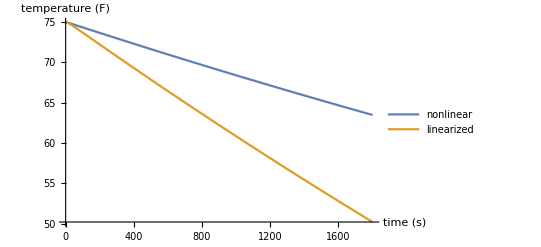

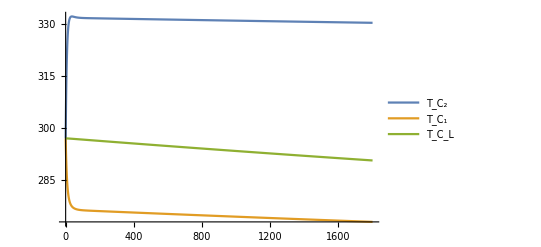

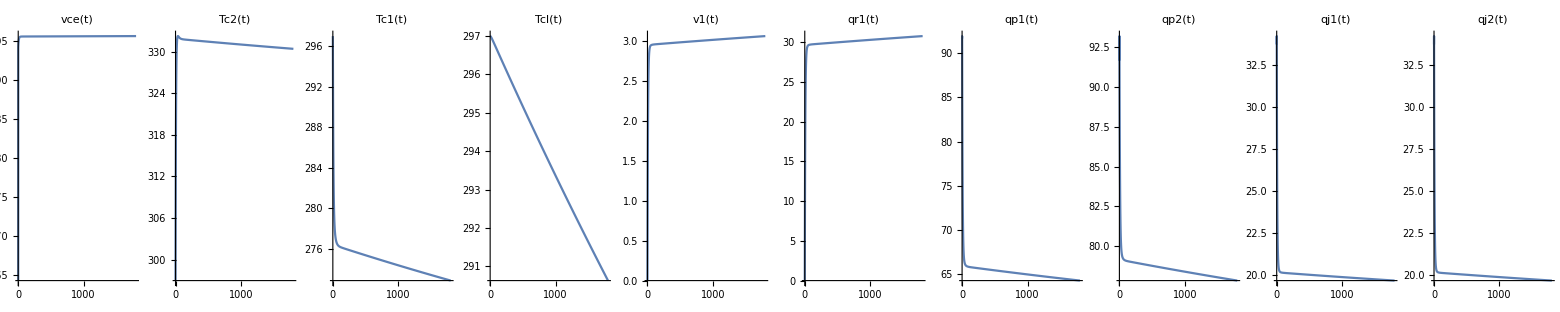

```mathematica
tlow=0;
thigh=60*30;
x00={0,297,297,297}; (* initial condition *)
nsysResponse=OutputResponse[{nsys//.params,x00},{12*UnitStep[t],297},{t,tlow,thigh}];
sysResponse=OutputResponse[{sys//.params//.op,x00},{12*UnitStep[t],297},{t,tlow,thigh}];
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
Plot[{nsysResponse[[4]],sysResponse[[4]]}*9/5-459.67//Evaluate,{t,tlow,thigh},PlotRange->All,PlotLegends->{"nonlinear","linearized"},AxesLabel->{"time (s)","temperature (F)"}]
Plot[nsysResponse[[2;;4]]//Evaluate,{t,tlow,thigh},PlotRange->All,PlotLegends->{"T_C_2","T_C_1","T_C_L"}]
Table[
Plot[nsysResponse[[i]],{t,tlow,thigh},PlotRange->All,PlotLabel->outExp[[i]]],
{i,1,m}
]//GraphicsRow[#,ImageSize->Full]&
```

We only show the linearized result for Tcl, but it’s not impressive. This presents a challenge for controller design based on this linearized version. It’s probably best to use the linearized version for controller design but the nonlinear version for simulation.

## Printing to Matlab (needs work)

The issue I’m having is getting Matlab to automatically generate a function file so I can ode45 it.
Once this is working, incorporate it into State as a function.

```mathematica
<<ToMatlab`
stateMatRep=Thread[stateVars->Table["x("<>ToString[i]<>")",{i,1,Length[stateVars]}]]~Join~
Thread[inVars->Table["u("<>ToString[i]<>")",{i,1,Length[inVars]}]]
myToMatlab[exp_]:=(exp/.stateMatRep//Map[ReplaceAll[#,x_[t_]:>x]&,#]&//ReplaceAll[#,α->a]&//ToMatlab//ToString);

matlabVars=stateEqList//Variables//ReplaceAll[#,α->a]&//Complement[#,stateVars~Join~inVars]&//Map[ReplaceAll[#,x_[t_]:>x]&,#]&;

(*{{"syms"}~Join~matlabVars}//Grid*)
For[i=1,i≤Length[matlabVars],i++,(matlabVars[[i]]//ToString)<>"=1; % dummy"//Print]
Length[stateVars]//Print["f=sym('f',["<>ToString[#]<>",1]);"]&;
Length[stateVars]//Print["x=sym('x',["<>ToString[#]<>",1]);"]&;
Length[inVars]//Print["u=sym('u',["<>ToString[#]<>",1]);"]&;

For[i=1,i≤Length[stateVars],i++,"f("<>ToString[i]<>")="<>(myToMatlab[stateEqList[[i]]])//Print]
```

c1=1; % dummy

c2=1; % dummy

ce=1; % dummy

cl=1; % dummy

r1=1; % dummy

r2=1; % dummy

r3=1; % dummy

rm=1; % dummy

rs=1; % dummy

2                         2                                              2                           2
    rm + rs      α        α          vce0    Tc10 α  -(2 r1 rm + 2 r3 rm)   Tc20 α     1     vce0 α   Tc10 α        vce0    Tc20 α    1     vce0 α   Tc20 α       1        1     Tc10 α     1              1        1
{{-(--------), -----, -(-----), 0}, {----- + ------, -------------------- - -------, ----- + ------ + -------, 0}, {----- - ------, ----- - ------ + -------, -(-----) - ----- - -------, -----}, {0, 0, -----, -(-----)}}
    ce rm rs   ce rm    ce rm        c2 rm   c2 rm      2 c2 r1 r3 rm        c2 rm   c2 r1   c2 rm     c2 rm        c1 rm   c1 rm   c1 r1   c1 rm     c1 rm     c1 r1    c1 r2    c1 rm   c1 r2          cl r2    cl r2=1; % dummy

f=sym('f',[4,1]);

x=sym('x',[4,1]);

u=sym('u',[2,1]);

f(1)=[u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(2).*ce.^(-2).*rm.^(-2).*rs.^(-1) ...
  .*(rm+rs)+x(3).*ce.^(-2).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1).*x(1).* ...
  ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-2).* ...
  rm.^(-2).*α+(-1).*x(3).*ce.^(-2).*rm.^(-2).*α,u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+(-1).* ...
  x(2).*ce.^(-2).*rm.^(-2).*α+x(3).*ce.^(-2).*rm.^(-2).*α,u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+ ...
  c2.^(-1).*rm.^(-1).*Tc10.*α)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*( ...
  c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α),u(1).*ce.^( ...
  -1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x( ...
  2).*ce.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^( ...
  -1).*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).* ...
  r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2),u(1).*ce.^(-1) ...
  .*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs);u(1) ...
  .*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...
  rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α),u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).* ...
  rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).* ...
  rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1) ...
  .*c1.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).* ...
  ((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1) ...
  .*rm.^(-1).*Tc10.*α.^2),x(2).*c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^( ...
  -1)+(-1).*x(3).*c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^( ...
  -1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs);u( ...
  1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...
  rm+rs),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs),x(2).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+( ...
  -1).*x(3).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),(-1).* ...
  x(2).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).*ce.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^( ...
  -1).*rm.^(-1).*rs.^(-1).*(rm+rs)];

f(2)=[x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1) ...
  .^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1) ...
  .*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*x(1).*x(3).*c2.^(-1).* ...
  ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1/2).*x(2).^2.*c2.^(-1).* ...
  ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+rs).^2+(1/2).*x(3).^2.*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+rs).^2,x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+(-1/2).*x( ...
  2).^2.*c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(1/2).*x(3).^2.*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*α.^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1) ...
  .*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*x( ...
  1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+(-1/2).*x(2).^2.*c2.^( ...
  -1).*ce.^(-2).*rm.^(-3).*α.^2+(1/2).*x(3).^2.*c2.^(-1).*ce.^(-2).* ...
  rm.^(-3).*α.^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+( ...
  1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm);x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).* ...
  vce0+c2.^(-1).*rm.^(-1).*Tc10.*α)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^( ...
  -1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α).^2+( ...
  1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^( ...
  -1).*rm.^(-1).*Tc10.*α).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1) ...
  .*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x( ...
  3).*c2.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1) ...
  .*rm.^(-1).*Tc20.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(( ...
  -1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.* ...
  rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2,x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+ ...
  c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1/2) ...
  .*x(2).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^( ...
  -1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2+(1/2).*x(3).^2.* ...
  c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.* ...
  α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2) ...
  .*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x( ...
  2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm); ...
  x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1/2) ...
  .*x(2).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2, ...
  x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+( ...
  1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).* ...
  rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1) ...
  .*c1.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^( ...
  -1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^( ...
  -1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c1.^(-2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c1.^( ...
  -2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+x(1).*x(3).*c1.^(-1).*c2.^(-1).* ...
  r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm);x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x( ...
  3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c2.^( ...
  -1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(1).*x(3).*c2.^(-1).*cl.^(-1).* ...
  r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c2.^( ...
  -1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(1).*x(3).*c2.^(-1).* ...
  cl.^(-1).*r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)];

f(3)=[x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^( ...
  -1).*rm.^(-1)+x(1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).* ...
  (rm+rs)+(1/2).*x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2).*( ...
  rm+rs).^2+(-1/2).*x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2) ...
  .*(rm+rs).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*ce.^(-1).* ...
  rm.^(-2).*α+(1/2).*x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+( ...
  -1/2).*x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2,x(2).*c1.^(-1) ...
  .*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+ ...
  x(1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+(1/2).*x(2).^2.*c1.^( ...
  -1).*ce.^(-2).*rm.^(-3).*α.^2+(-1/2).*x(3).^2.*c1.^(-1).*ce.^(-2) ...
  .*rm.^(-3).*α.^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2) ...
  .*x(1).^2.*c1.^(-1).*rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1) ...
  .*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).* ...
  r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).* ...
  c1.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).* ...
  Tc10.*α)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).* ...
  vce0+c2.^(-1).*rm.^(-1).*Tc10.*α).^2+(-1/2).*x(3).^2.*c1.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*((-1/2).* ...
  c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1) ...
  .*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^( ...
  -1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+(-1/2).*x(3) ...
  .^2.*c1.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^( ...
  -1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2) ...
  .^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^( ...
  -1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(2).* ...
  c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).* ...
  rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(1/2) ...
  .*x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^( ...
  -1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*(c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*((-1).* ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2) ...
  .*x(1).^2.*c1.^(-1).*rm.^(-1)+(1/2).*x(2).^2.*c1.^(-3).*r2.^(-2).* ...
  rm.^(-1)+(-1/2).*x(3).^2.*c1.^(-3).*r2.^(-2).*rm.^(-1)+(-1).*x(1) ...
  .*x(2).*c1.^(-2).*r2.^(-1).*rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3) ...
  .*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^( ...
  -1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1),x(2).*c1.^(-1).* ...
  r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)) ...
  +x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1),x(2) ...
  .*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).* ...
  rm.^(-1)+(1/2).*x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+( ...
  -1/2).*x(3).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(1) ...
  .*x(2).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1),x(2).*c1.^(-1).* ...
  r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)) ...
  +x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+(1/2) ...
  .*x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1/2).*x(3) ...
  .^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(1).*x(2).*c1.^(-1).* ...
  cl.^(-1).*r2.^(-1).*rm.^(-1)];

f(4)=x(3).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);

{vce[t]→x(1),Tc2[t]→x(2),Tc1[t]→x(3),Tcl[t]→x(4),vs[t]→u(1),Ta[t]→u(2)}

c1=1; % dummy

c2=1; % dummy

ce=1; % dummy

cl=1; % dummy

r1=1; % dummy

r2=1; % dummy

r3=1; % dummy

rm=1; % dummy

rs=1; % dummy

2                         2                                              2                           2
    rm + rs      α        α          vce0    Tc10 α  -(2 r1 rm + 2 r3 rm)   Tc20 α     1     vce0 α   Tc10 α        vce0    Tc20 α    1     vce0 α   Tc20 α       1        1     Tc10 α     1              1        1
{{-(--------), -----, -(-----), 0}, {----- + ------, -------------------- - -------, ----- + ------ + -------, 0}, {----- - ------, ----- - ------ + -------, -(-----) - ----- - -------, -----}, {0, 0, -----, -(-----)}}
    ce rm rs   ce rm    ce rm        c2 rm   c2 rm      2 c2 r1 r3 rm        c2 rm   c2 r1   c2 rm     c2 rm        c1 rm   c1 rm   c1 r1   c1 rm     c1 rm     c1 r1    c1 r2    c1 rm   c1 r2          cl r2    cl r2=1; % dummy

f=sym('f',[4,1]);

x=sym('x',[4,1]);

u=sym('u',[2,1]);

f(1)=[u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(2).*ce.^(-2).*rm.^(-2).*rs.^(-1) ...
  .*(rm+rs)+x(3).*ce.^(-2).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1).*x(1).* ...
  ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-2).* ...
  rm.^(-2).*α+(-1).*x(3).*ce.^(-2).*rm.^(-2).*α,u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+(-1).* ...
  x(2).*ce.^(-2).*rm.^(-2).*α+x(3).*ce.^(-2).*rm.^(-2).*α,u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs);u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^( ...
  -1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+ ...
  c2.^(-1).*rm.^(-1).*Tc10.*α)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*( ...
  c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α),u(1).*ce.^( ...
  -1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x( ...
  2).*ce.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^( ...
  -1).*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).* ...
  rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c2.^(-1).* ...
  r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.* ...
  α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1) ...
  .*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2),u(1).*ce.^(-1) ...
  .*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs);u(1) ...
  .*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...
  rm+rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1).*x(3).*ce.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α),u(1).* ...
  ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+ ...
  rs)+x(2).*ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).* ...
  rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2)+(-1).*x(3).* ...
  ce.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2),u(1).*ce.^(-1).*rs.^(-1)+( ...
  -1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs)+x(2).*ce.^(-1).* ...
  rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1) ...
  .*c1.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1).*x(3).*ce.^(-1).*rm.^(-1).* ...
  ((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1) ...
  .*rm.^(-1).*Tc10.*α.^2),x(2).*c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^( ...
  -1)+(-1).*x(3).*c1.^(-1).*ce.^(-1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^( ...
  -1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs);u( ...
  1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...
  rm+rs),u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).* ...
  rs.^(-1).*(rm+rs),x(2).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+( ...
  -1).*x(3).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).* ...
  rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*(rm+rs),(-1).* ...
  x(2).*ce.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1)+x(3).*ce.^(-1).*cl.^( ...
  -1).*r2.^(-1).*rm.^(-1)+u(1).*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^( ...
  -1).*rm.^(-1).*rs.^(-1).*(rm+rs)];

f(2)=[x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1) ...
  .^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1) ...
  .*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*x(1).*x(3).*c2.^(-1).* ...
  ce.^(-1).*rm.^(-2).*rs.^(-1).*(rm+rs)+(-1/2).*x(2).^2.*c2.^(-1).* ...
  ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+rs).^2+(1/2).*x(3).^2.*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*rs.^(-2).*(rm+rs).^2,x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+(-1/2).*x( ...
  2).^2.*c2.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+(1/2).*x(3).^2.*c2.^(-1) ...
  .*ce.^(-2).*rm.^(-3).*α.^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1) ...
  .*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*x( ...
  1).*x(3).*c2.^(-1).*ce.^(-1).*rm.^(-2).*α+(-1/2).*x(2).^2.*c2.^( ...
  -1).*ce.^(-2).*rm.^(-3).*α.^2+(1/2).*x(3).^2.*c2.^(-1).*ce.^(-2).* ...
  rm.^(-3).*α.^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+( ...
  1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm);x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).* ...
  vce0+c2.^(-1).*rm.^(-1).*Tc10.*α)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^( ...
  -1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α).^2+( ...
  1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^( ...
  -1).*rm.^(-1).*Tc10.*α).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1) ...
  .*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^( ...
  -1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x( ...
  3).*c2.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).* ...
  r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1) ...
  .*rm.^(-1).*Tc20.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(( ...
  -1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.* ...
  rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2,x(3).*c2.^(-1).*r1.^( ...
  -1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+( ...
  -1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+ ...
  c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1/2) ...
  .*x(2).^2.*c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^( ...
  -1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2+(1/2).*x(3).^2.* ...
  c2.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.* ...
  α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2) ...
  .*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x( ...
  2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm); ...
  x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(-1/2) ...
  .*x(2).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1) ...
  .*(c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α).^2, ...
  x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).* ...
  rm.^(-1).*Tc20.*α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^(-1).*(c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1) ...
  .*Tc20.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^(-1).*(c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+( ...
  1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1) ...
  .*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+x(1).*x(3).*c2.^(-1).* ...
  rm.^(-1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1) ...
  .*c1.^(-1).*rm.^(-1).*Tc10.*α.^2)+(-1/2).*x(2).^2.*c2.^(-1).*rm.^( ...
  -1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2).^2+(1/2).*x(3).^2.*c2.^(-1).*rm.^( ...
  -1).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c1.^(-2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c1.^( ...
  -2).*c2.^(-1).*r2.^(-2).*rm.^(-1)+x(1).*x(3).*c1.^(-1).*c2.^(-1).* ...
  r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm);x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x( ...
  3).*c2.^(-1).*r1.^(-1)+u(2).*c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.* ...
  c2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c2.^( ...
  -1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(1).*x(3).*c2.^(-1).*cl.^(-1).* ...
  r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm),x(3).*c2.^(-1).*r1.^(-1)+u(2).* ...
  c2.^(-1).*r3.^(-1)+(1/2).*x(1).^2.*c2.^(-1).*rm.^(-1)+(-1/2).*x(2) ...
  .^2.*c2.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(1/2).*x(3).^2.*c2.^( ...
  -1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(1).*x(3).*c2.^(-1).* ...
  cl.^(-1).*r2.^(-1).*rm.^(-1)+(-1/2).*x(2).*c2.^(-1).*r1.^(-1).* ...
  r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)];

f(3)=[x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).* ...
  c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^( ...
  -1).*rm.^(-1)+x(1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*rs.^(-1).* ...
  (rm+rs)+(1/2).*x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2).*( ...
  rm+rs).^2+(-1/2).*x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*rs.^(-2) ...
  .*(rm+rs).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*ce.^(-1).* ...
  rm.^(-2).*α+(1/2).*x(2).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2+( ...
  -1/2).*x(3).^2.*c1.^(-1).*ce.^(-2).*rm.^(-3).*α.^2,x(2).*c1.^(-1) ...
  .*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^( ...
  -1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+ ...
  x(1).*x(2).*c1.^(-1).*ce.^(-1).*rm.^(-2).*α+(1/2).*x(2).^2.*c1.^( ...
  -1).*ce.^(-2).*rm.^(-3).*α.^2+(-1/2).*x(3).^2.*c1.^(-1).*ce.^(-2) ...
  .*rm.^(-3).*α.^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2) ...
  .*x(1).^2.*c1.^(-1).*rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1) ...
  .*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).* ...
  r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).* ...
  c1.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).* ...
  Tc10.*α)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*rm.^(-1).* ...
  vce0+c2.^(-1).*rm.^(-1).*Tc10.*α).^2+(-1/2).*x(3).^2.*c1.^(-1).* ...
  rm.^(-1).*(c2.^(-1).*rm.^(-1).*vce0+c2.^(-1).*rm.^(-1).*Tc10.*α) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*((-1/2).* ...
  c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1) ...
  .*c2.^(-1).*rm.^(-1).*Tc20.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^( ...
  -1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).*rm.^(-1).*(2.*r1.*rm+ ...
  2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.*α.^2).^2+(-1/2).*x(3) ...
  .^2.*c1.^(-1).*rm.^(-1).*((-1/2).*c2.^(-1).*r1.^(-1).*r3.^(-1).* ...
  rm.^(-1).*(2.*r1.*rm+2.*r3.*rm)+(-1).*c2.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c2.^(-1).*r1.^(-1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1) ...
  .*Tc10.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^( ...
  -1)+c2.^(-1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2) ...
  .^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*(c2.^(-1).*r1.^(-1)+c2.^( ...
  -1).*rm.^(-1).*vce0.*α+c2.^(-1).*rm.^(-1).*Tc10.*α.^2).^2,x(2).* ...
  c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1) ...
  .*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).* ...
  rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1) ...
  .^2.*c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*( ...
  c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α)+(1/2) ...
  .*x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).* ...
  c1.^(-1).*rm.^(-1).*Tc20.*α).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^( ...
  -1).*(c1.^(-1).*rm.^(-1).*vce0+(-1).*c1.^(-1).*rm.^(-1).*Tc20.*α) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*(c1.^(-1) ...
  .*r1.^(-1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).* ...
  Tc20.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^( ...
  -1)+(-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.* ...
  α.^2).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*(c1.^(-1).*r1.^(-1)+ ...
  (-1).*c1.^(-1).*rm.^(-1).*vce0.*α+c1.^(-1).*rm.^(-1).*Tc20.*α.^2) ...
  .^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1) ...
  .*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.* ...
  c1.^(-1).*rm.^(-1)+(-1).*x(1).*x(2).*c1.^(-1).*rm.^(-1).*((-1).* ...
  c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^( ...
  -1).*Tc10.*α.^2)+(1/2).*x(2).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2).^2+(-1/2).*x(3).^2.*c1.^(-1).*rm.^(-1).*((-1).*c1.^( ...
  -1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)+(-1).*c1.^(-1).*rm.^(-1).* ...
  Tc10.*α.^2).^2,x(2).*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).* ...
  r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2) ...
  .*x(1).^2.*c1.^(-1).*rm.^(-1)+(1/2).*x(2).^2.*c1.^(-3).*r2.^(-2).* ...
  rm.^(-1)+(-1/2).*x(3).^2.*c1.^(-3).*r2.^(-2).*rm.^(-1)+(-1).*x(1) ...
  .*x(2).*c1.^(-2).*r2.^(-1).*rm.^(-1);x(2).*c1.^(-1).*r1.^(-1)+x(3) ...
  .*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1))+x(4).*c1.^( ...
  -1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1),x(2).*c1.^(-1).* ...
  r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)) ...
  +x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1),x(2) ...
  .*c1.^(-1).*r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^( ...
  -1).*r2.^(-1))+x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).* ...
  rm.^(-1)+(1/2).*x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+( ...
  -1/2).*x(3).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1).*x(1) ...
  .*x(2).*c1.^(-1).*cl.^(-1).*r2.^(-1).*rm.^(-1),x(2).*c1.^(-1).* ...
  r1.^(-1)+x(3).*((-1).*c1.^(-1).*r1.^(-1)+(-1).*c1.^(-1).*r2.^(-1)) ...
  +x(4).*c1.^(-1).*r2.^(-1)+(1/2).*x(1).^2.*c1.^(-1).*rm.^(-1)+(1/2) ...
  .*x(2).^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+(-1/2).*x(3) ...
  .^2.*c1.^(-1).*cl.^(-2).*r2.^(-2).*rm.^(-1)+x(1).*x(2).*c1.^(-1).* ...
  cl.^(-1).*r2.^(-1).*rm.^(-1)];

f(4)=x(3).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);

a=1; % dummy
c1=1; % dummy
c2=1; % dummy
ce=1; % dummy
cl=1; % dummy
r1=1; % dummy
r2=1; % dummy
r3=1; % dummy
rm=1; % dummy
rs=1; % dummy
f=sym('f',[4,1]);
x=sym('x',[4,1]);
u=sym('u',[1,1]);
f(1)=(-1).*x(2).*a.*ce.^(-1).*rm.^(-1)+x(3).*a.*ce.^(-1).*rm.^(-1)+u(1) ...\n  .*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...\n  rm+rs);\n
f(2)=x(3).*c1.^(-1).*r1.^(-1)+x(4).*c1.^(-1).*r2.^(-1)+x(1).*(x(2).*a.* ...\n  c1.^(-1).*rm.^(-1)+(-1).*x(3).*a.*c1.^(-1).*rm.^(-1))+x(2).*(c1.^( ...\n  -1).*r1.^(-1).*((-1).*r1+(-1).*r2).*r2.^(-1)+(-2).*x(3).*a.^2.* ...\n  c1.^(-1).*rm.^(-1))+x(2).^2.*a.^2.*c1.^(-1).*rm.^(-1)+x(3).^2.* ...\n  a.^2.*c1.^(-1).*rm.^(-1);\n
f(3)=x(3).*c2.^(-1).*r1.^(-1).*((-1).*r1+(-1).*r3).*r3.^(-1)+x(1).*(( ...\n  -1).*x(2).*a.*c2.^(-1).*rm.^(-1)+x(3).*a.*c2.^(-1).*rm.^(-1))+x(2) ...\n  .*(c2.^(-1).*r1.^(-1)+2.*x(3).*a.^2.*c2.^(-1).*rm.^(-1))+(-1).*x( ...\n  2).^2.*a.^2.*c2.^(-1).*rm.^(-1)+(-1).*x(3).^2.*a.^2.*c2.^(-1).* ...\n  rm.^(-1);\n
f(4)=x(2).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);\n